Risk Plots

## Unconstrained solutions

Plots that show the boundary of the feasible set, then draw in traces of solutions for iid mean process (typical of spike-and-slab Bayesian model).

Transfer file from server.  Parsing of parameter values, with special cases... 
	alpha = defines oracle		 					0 mins LS risk, and 1 mins risk, and other mins testimator risk
	beta = rate used by bidder if geometric				0 for universal (if omega=0, then bid = beta/n)
	omega = payout for each player					0 indicates fixed bid (ie, old fashioned), 1 means unconstrained
	scale = scale parameter of universal distribution

### Functions for plotting and reading data ...

Idea is to make a file name based on parameter values.  Keep the name and parameter values as the first two items in a list with the data last.

```mathematica
Clear[fmt,makeID,  getAlpha, getBeta,getN, getOmegaAlpha,getOmegaBeta, getData];

fmt[x_]:=With[{s= ToString[Round[100x]]},
If[StringLength[s]>1,s,StringJoin["0",s]]
]

makeID[α_,ωα_,β_,ωβ_, scale_, n_] :=
{StringJoin["summary_risk_alpha",fmt[α],"_",fmt[ωα],"_beta",fmt[β],"_",fmt[ωβ] ,
"_scale",ToString[scale],"_n",ToString[n]],
{α,ωα,β,ωβ,scale,n}
}

getAlpha[{_,parms_,_}] :=getAlpha[parms]
getAlpha[{α_,_,_,_,_,_}] :=α

getBeta[{_,parms_,_}] :=getBeta[parms]
getBeta[{_,_,β_,_,_,_}] :=β

getN[{_,parms_,_}] :=getN[parms]
getN[{_,_,_,_,_,n_}] :=n

getOmegaAlpha[{_,parms_,_}]:=getOmegaAlpha[parms]
getOmegaAlpha[{_,ω_,_,_,_,_}]:=ω

getOmegaBeta[{_,parms_,_}]:=getOmegaBeta[parms]
getOmegaBeta[{_,_,_,ω_,_,_}]:=ω


getData[{name_,parms_},figureNumber_,server_]:=Module[
{f=ToString[figureNumber],
fullName,x},
fullName=StringJoin[" ~/C/bellman/figures/f",f,"/",name];
If[StringLength[server]>1,
<<(StringJoin["!scp ",server,"C/bellman/figures/f",f,"/",name, fullName])];
x= Import[StringJoin["~/C/bellman/figures/f",f,"/",name], "Table"];
Print["Dimensions ", Dimensions[x]];
{name,parms,Sort[x,#1⟦3⟧<#2⟦3⟧&]} (* sort on angle *)
]
```

The function pickColumns adds 1 and flips sign to make work with log/log plot.

```mathematica
Clear[pickColumns, playerName,drawFeasibleSet,drawLogFeasibleSet];

pickColumns[simres_] :=With[
{cols = If[Length[First[simres]]<8,{5,6},{7,8}]},
 1 -(#⟦cols⟧&)/@ simres
]

playerName[list_List] := playerName[list⟦1⟧,list⟦2⟧];
playerName[α_,0] := StringJoin["Bonferroni(",ToString[α],")"]
playerName[0,1] := "Least Squares";
playerName[1,1] := "RI Oracle"
playerName[α_,1] := StringJoin["Oracle(",ToString[α],")"]
playerName[α_,ω_] := StringJoin["Geom(",ToString[α],",",ToString[ω],")"]

drawFeasibleSet[{name_,{α_,ω1_,β_,ω2_,σ_,n_},simres_},{join_:False,color_:Blue}]:=Module[
{xy =pickColumns[simres]},
ListPlot[xy,
Joined->join,
AspectRatio->1,
PlotStyle->{color,PointSize[0.015]},
AxesLabel->{playerName[α,ω1],playerName[β,ω2]},
PlotLabel->StringJoin["Feasible Risks  n=",ToString[n],", ω=",ToString[ω2],")"],
BaseStyle->{Gray,Larger,FontFamily->"Chalkboard",FontSize->10},
Epilog->{Orange,Line[{{0.0,0.0},{1000,1000}}] }
]
]

drawLogFeasibleSet[{name_,{α_,ω1_,β_,ω2_,σ_,n_},simres_},{join_:False,color_:Blue}] := Module[
{xy=pickColumns[simres]},
ListLogLogPlot[xy,
Print["2 log n =",2.Log[n]];
Joined->join,
PlotRange->{{1,1.2Max[xy]},{1,1.15Max[xy]}},
AspectRatio->1,
PlotStyle->{color,PointSize[0.015]},
AxesLabel->{playerName[α,ω1],playerName[β,ω2]},
PlotLabel->StringJoin["Feasible Risks  n=",ToString[n],", ω=",ToString[ω2],")"],
BaseStyle->{Black,Larger,FontFamily->"Chalkboard",FontSize->10}, 
Epilog->{ (* LogLogPlot exponentiates all before drawing, as if these are on log scale *)
Orange,Line[{{0.01,0.01},{100,100}}],
Red, Line[{{0,Log[1+2Log[n]]},{Log[20000],Log[20000+20000(2Log [n])]}}],
color,(*Arrow[Log[xy]]*)}]
]
```

```mathematica
Clear[drawFeasibleSets];

drawFeasibleSets[simres_List, title_,labels_]:=Module[
{xy =(pickColumns[#⟦3⟧]&)/@simres,
colors=GrayLevel/@Range[0.7,0.3,-0.4/Length[simres]],
legend= getOmegaBeta/@simres
},
ListPlot[xy,
Joined->True,
AspectRatio->1,
PlotStyle->colors,AxesLabel->labels,PlotLabel-> title,
BaseStyle->{Black,Larger,FontFamily->"Chalkboard",FontSize->12},
PlotLegends->SwatchLegend[legend, LegendLabel-> "ω"],
Epilog->{Orange,Line[{{0.0,0.0},{1000,1000}}] }
]
]
```

### Figure 1 Feasible risks for varying ω_β, with RI oracle

The data that is produced has a list of 3 items
	file name
	parameter values (as alpha, beta, omega, scale and n)
	simulation results.

```mathematica
id = With[
{α=1,ωα=1,β=0.1,scale=2,n=500},
makeID[α,ωα,β,#,scale,n]&/@ {0.05,0.25,0.50,0.75}
]

f1Data=Table[getData[id⟦i⟧,1,""],{i,1,4}];
```

{{summary_risk_alpha100_100_beta10_05_scale2_n500,{1,1,0.1,0.05,2,500}},{summary_risk_alpha100_100_beta10_25_scale2_n500,{1,1,0.1,0.25,2,500}},{summary_risk_alpha100_100_beta10_50_scale2_n500,{1,1,0.1,0.5,2,500}},{summary_risk_alpha100_100_beta10_75_scale2_n500,{1,1,0.1,0.75,2,500}}}

Dimensions {58,8}

Dimensions {58,8}

Dimensions {58,8}

«1 more identical outputs»

Look for the angle where risk increases suddenly.

```mathematica
f1Data[[4,3]]//TableForm
```

Oracle(1,1) | Geom(0.1) | 0 | 0.75 | 500 | -14.3051 | 0 | -14.3051
Oracle(1,1) | Geom(0.1) | 15 | 0.75 | 500 | -13.8176 | 0 | -14.3051
Oracle(1,1) | Geom(0.1) | 30 | 0.75 | 500 | -12.3886 | 0 | -14.3051
Oracle(1,1) | Geom(0.1) | 45 | 0.75 | 500 | -10.1152 | 0 | -14.3051
Oracle(1,1) | Geom(0.1) | 60 | 0.75 | 500 | -7.15254 | 0 | -14.3051
Oracle(1,1) | Geom(0.1) | 65 | 0.75 | 500 | -6.04559 | 0 | -14.3051
Oracle(1,1) | Geom(0.1) | 70 | 0.75 | 500 | -4.89262 | 0 | -14.3051
Oracle(1,1) | Geom(0.1) | 75 | 0.75 | 500 | -3.70243 | 0 | -14.3051
Oracle(1,1) | Geom(0.1) | 80 | 0.75 | 500 | -2.48405 | 0 | -14.3051
Oracle(1,1) | Geom(0.1) | 85 | 0.75 | 500 | -1.24677 | 0 | -14.3051
Oracle(1,1) | Geom(0.1) | 90 | 0.75 | 500 | 7.30079×10^-11 | 0 | -14.3051
Oracle(1,1) | Geom(0.1) | 91 | 0.75 | 500 | 0.249658 | 0 | -14.3051
Oracle(1,1) | Geom(0.1) | 92 | 0.75 | 500 | 0.49924 | 0 | -14.3051
Oracle(1,1) | Geom(0.1) | 93 | 0.75 | 500 | 0.74867 | 0 | -14.3051
Oracle(1,1) | Geom(0.1) | 93.2 | 0.75 | 500 | 0.798531 | 0 | -14.3051
Oracle(1,1) | Geom(0.1) | 93.4 | 0.75 | 500 | 0.848382 | 0 | -14.3051
Oracle(1,1) | Geom(0.1) | 93.6 | 0.75 | 500 | 0.898223 | 0 | -14.3051
Oracle(1,1) | Geom(0.1) | 93.8 | 0.75 | 500 | 1.18421 | -6.136 | -110.25
Oracle(1,1) | Geom(0.1) | 94 | 0.75 | 500 | 1.59278 | -6.94952 | -122.216
Oracle(1,1) | Geom(0.1) | 94.2 | 0.75 | 500 | 2.01713 | -7.40804 | -128.42
Oracle(1,1) | Geom(0.1) | 94.4 | 0.75 | 500 | 2.50719 | -8.12864 | -138.321
Oracle(1,1) | Geom(0.1) | 94.6 | 0.75 | 500 | 3.0041 | -8.68341 | -145.383
Oracle(1,1) | Geom(0.1) | 94.8 | 0.75 | 500 | 3.52449 | -9.2506 | -152.282
Oracle(1,1) | Geom(0.1) | 95 | 0.75 | 500 | 4.06789 | -9.80699 | -158.768
Oracle(1,1) | Geom(0.1) | 95.2 | 0.75 | 500 | 4.63378 | -10.3701 | -165.075
Oracle(1,1) | Geom(0.1) | 95.4 | 0.75 | 500 | 5.2224 | -10.9763 | -171.611
Oracle(1,1) | Geom(0.1) | 95.6 | 0.75 | 500 | 5.81414 | -11.5174 | -177.045
Oracle(1,1) | Geom(0.1) | 95.8 | 0.75 | 500 | 6.46475 | -12.2099 | -184.176
Oracle(1,1) | Geom(0.1) | 96 | 0.75 | 500 | 7.12202 | -12.8613 | -190.502
Oracle(1,1) | Geom(0.1) | 96.2 | 0.75 | 500 | 7.79892 | -13.518 | -196.648
Oracle(1,1) | Geom(0.1) | 96.4 | 0.75 | 500 | 8.49706 | -14.1934 | -202.765
Oracle(1,1) | Geom(0.1) | 96.6 | 0.75 | 500 | 9.21655 | -14.8849 | -208.834
Oracle(1,1) | Geom(0.1) | 96.8 | 0.75 | 500 | 9.95729 | -15.597 | -214.897
Oracle(1,1) | Geom(0.1) | 97 | 0.75 | 500 | 10.719 | -16.3168 | -220.845
Oracle(1,1) | Geom(0.1) | 98 | 0.75 | 500 | 14.8389 | -20.229 | -250.559
Oracle(1,1) | Geom(0.1) | 99 | 0.75 | 500 | 19.4771 | -24.5279 | -279.369
Oracle(1,1) | Geom(0.1) | 100 | 0.75 | 500 | 24.6059 | -29.1872 | -307.229
Oracle(1,1) | Geom(0.1) | 105 | 0.75 | 500 | 56.9197 | -55.4599 | -426.9
Oracle(1,1) | Geom(0.1) | 110 | 0.75 | 500 | 98.0903 | -82.3961 | -513.179
Oracle(1,1) | Geom(0.1) | 115 | 0.75 | 500 | 146.268 | -111.039 | -584.224
Oracle(1,1) | Geom(0.1) | 120 | 0.75 | 500 | 198.04 | -131.46 | -623.776
Oracle(1,1) | Geom(0.1) | 125 | 0.75 | 500 | 252.159 | -153.283 | -658.535
Oracle(1,1) | Geom(0.1) | 135 | 0.75 | 500 | 361.891 | -184.777 | -696.57
Oracle(1,1) | Geom(0.1) | 150 | 0.75 | 500 | 517.155 | -224.65 | -726.86
Oracle(1,1) | Geom(0.1) | 165 | 0.75 | 500 | 649.185 | -263.726 | -742.75
Oracle(1,1) | Geom(0.1) | 180 | 0.75 | 500 | 745.825 | -298.903 | -745.825
Oracle(1,1) | Geom(0.1) | 195 | 0.75 | 500 | 800.539 | -320.718 | -742.841
Oracle(1,1) | Geom(0.1) | 210 | 0.75 | 500 | 807.025 | -346.256 | -731.961
Oracle(1,1) | Geom(0.1) | 225 | 0.75 | 500 | 768.659 | -397.498 | -689.551
Oracle(1,1) | Geom(0.1) | 240 | 0.75 | 500 | 706.294 | -482.395 | -577.055
Oracle(1,1) | Geom(0.1) | 255 | 0.75 | 500 | 623.122 | -500 | -541.535
Oracle(1,1) | Geom(0.1) | 270 | 0.75 | 500 | 500 | -500 | -500.035
Oracle(1,1) | Geom(0.1) | 285 | 0.75 | 500 | 353.552 | -500 | -500
Oracle(1,1) | Geom(0.1) | 300 | 0.75 | 500 | 183.013 | -500 | -500
Oracle(1,1) | Geom(0.1) | 315 | 0.75 | 500 | -1.26286×10^-8 | -500 | -500
Oracle(1,1) | Geom(0.1) | 330 | 0.75 | 500 | -12.3841 | -0.0452785 | -14.3261
Oracle(1,1) | Geom(0.1) | 345 | 0.75 | 500 | -13.8175 | -0.00219221 | -14.3055
Oracle(1,1) | Geom(0.1) | 359 | 0.75 | 500 | -14.3029 | 0 | -14.3051

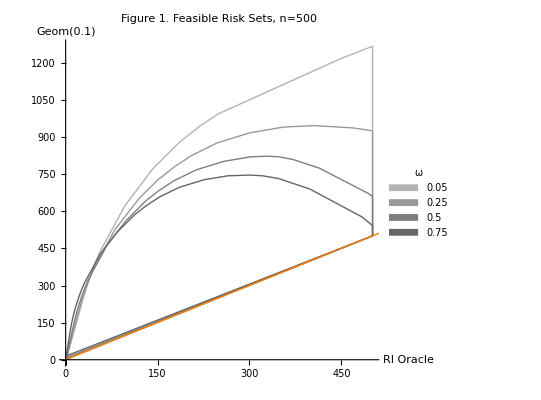

```mathematica
With[{β=ToString[getBeta[f1Data⟦1⟧]]},
drawFeasibleSets[f1Data, 
"Figure 1. Feasible Risk Sets, n=500",
{"RI Oracle",StringJoin["Geom(",β,")"]}]
]
```

Comments on log scale plot:
	Log version for small risks; add one to everything to be logable.  
	Add 1 as in the F&G paper for the forced estimation of an intercept. 
	Feasible set is not convex in this new coordinate system...

```mathematica
colors=GrayLevel /@ {0.2,0.4,0.6,0.8};
f1LogPlots=Table[drawLogFeasibleSet[f1Data⟦i⟧,{False,colors⟦i⟧}],{i,1,4}];
```

2 log n =12.4292

2 log n =12.4292

2 log n =12.4292

«1 more identical outputs»

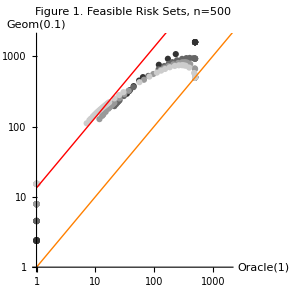

```mathematica
Show[f1LogPlots,PlotLabel->"Figure 1. Feasible Risk Sets, n=500"]
```

### Figure 2 Feasible risks for varying ω_β, with testimator oracle

```mathematica
id = With[
{α=0.1,ωα=1,β=0.1,scale=2,n=500},
makeID[α,ωα,β,#,scale,n]&/@ {0.05,0.25,0.50,0.75}
]

f2Data=Table[getData[id⟦i⟧,2,""],{i,1,4}];
```

{{summary_risk_alpha10_100_beta10_05_scale2_n500,{0.1,1,0.1,0.05,2,500}},{summary_risk_alpha10_100_beta10_25_scale2_n500,{0.1,1,0.1,0.25,2,500}},{summary_risk_alpha10_100_beta10_50_scale2_n500,{0.1,1,0.1,0.5,2,500}},{summary_risk_alpha10_100_beta10_75_scale2_n500,{0.1,1,0.1,0.75,2,500}}}

Dimensions {42,8}

Dimensions {42,8}

Dimensions {42,8}

«1 more identical outputs»

Look for the angle where risk increases suddenly.

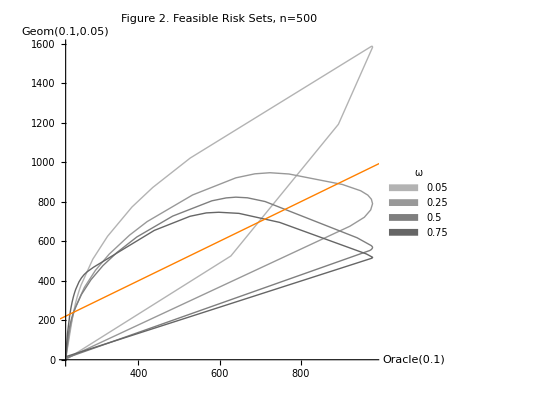

```mathematica
drawFeasibleSets[f2Data, 
"Figure 2. Feasible Risk Sets, n=500",
{playerName[f2Data⟦1,2,{1,2}⟧],playerName[f2Data⟦1,2,{3,4}⟧]}
]
```

Log scale is less interesting for these having seen them for the prior example.

```mathematica
f2LogPlots=Table[drawLogFeasibleSet[f2Data⟦i⟧,{False,colors⟦i⟧}],{i,1,4}]
```

```mathematica
Show[f2LogPlots,PlotLabel->"Figure 1. Feasible Risk Sets, n=500"]
```

### Figure 3 Paths within the feasible set, illustrating shape

This figure shows paths within the feasible set produced by non-zero means that occur with varying probabilities and varying sizes. The concave shape of the path within the feasible set shows that we are only gettin the convex boundary.  The figures require the data from figure 2 to show the boundary, then put these paths within that set.

```mathematica
stripCol[x_]:= #⟦{2,3}⟧&/@x

With[
{α=0.10,β=0.10,ω=0.5,scale=2,n=500},
With[
{path=StringJoin["~/C/bellman/figures/f3/risk_alpha",fmt[α],"_beta",fmt[β],"_omega",fmt[ω],"_scale",ToString[scale],"_n",ToString[n]]},
Print[StringJoin[path,"/m0.5"]];
rr[0.5]=-stripCol[Import[StringJoin[path,"/m0.5"], "Table"]];
rr[1.0]=-stripCol[Import[StringJoin[path,"/m1.0"], "Table"]];
rr[1.5]=-stripCol[Import[StringJoin[path,"/m1.5"], "Table"]];
rr[2.0]=-stripCol[Import[StringJoin[path,"/m2.0"], "Table"]];
rr[2.5]=-stripCol[Import[StringJoin[path,"/m2.5"], "Table"]];
rr[3.0]=-stripCol[Import[StringJoin[path,"/m3.0"], "Table"]];
rr[3.5]=-stripCol[Import[StringJoin[path,"/m3.5"], "Table"]];
rr[4.0]=-stripCol[Import[StringJoin[path,"/m4.0"], "Table"]];
]
]
```

~/C/bellman/figures/f3/risk_alpha10_beta10_omega50_scale2_n500/m0.5

Now add the data for the 2 - point distribution with pZero signal.  Take off the leading pZero column, leaving oracle and bidder risks.

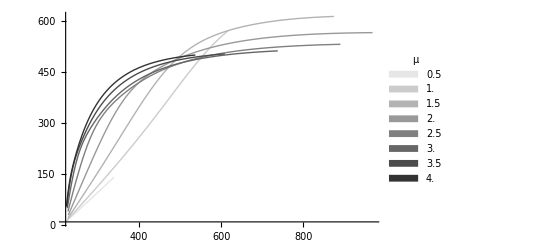

```mathematica
With[
{μ={0.5,1.0,1.5,2.0,2.5,3.0,3.5,4.0}},
lp=ListPlot[rr/@μ,
PlotRange->All,
Joined->True,PlotLegends->SwatchLegend[μ,LegendLabel->"μ"],
PlotStyle->GrayLevel/@Range[0.9,0.1,-0.1]]
]
```

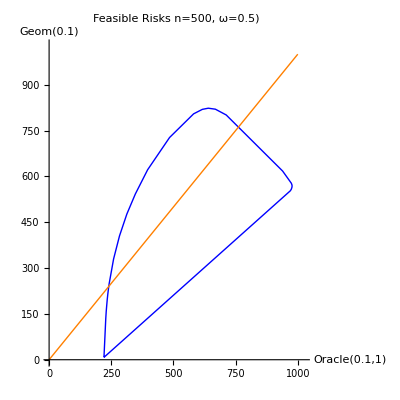

```mathematica
fp=drawFeasibleSet[f2Data⟦3⟧,{True,Blue}]
```

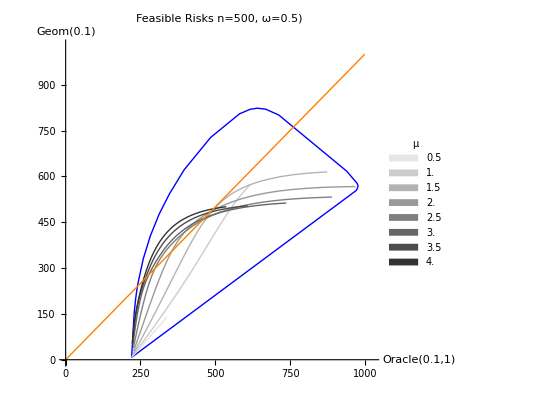

```mathematica
Show[fp,lp]
```

### Figure 4 Comparison of bidders with different ω

```mathematica
id =With[
{α=0.1,ω1=0.05,β=0.1,ω2=0.50,scale=2,n=40},
makeID[α,ω1,β,ω2,scale,n]
]

f4Data = getData[id,4,""];
```

{summary_risk_alpha10_05_beta10_50_scale2_n40,{0.1,0.05,0.1,0.5,2,40}}

Dimensions {34,12}

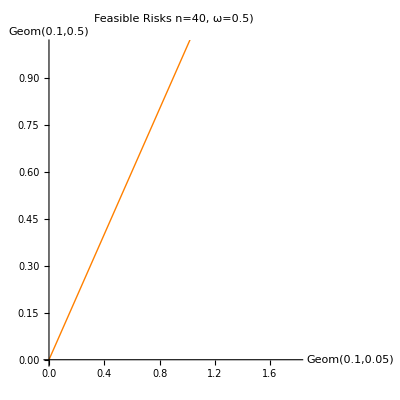

```mathematica
drawFeasibleSet[f4Data,{True,Blue}]
```

```mathematica
f4Data
```

{summary_risk_alpha10_05_beta10_50_scale2_n40,{0.1,0.05,0.1,0.5,2,40},{{Geom(0.1),Geom(0.1),0,2,0.1,0.05,0.1,0.5,.risk,-5.61642,-0.872671,-5.61642},{Geom(0.1),Geom(0.1),15,2,0.1,0.05,0.1,0.5,.risk,-5.64037,-0.758307,-5.63616},{Geom(0.1),Geom(0.1),30,2,0.1,0.05,0.1,0.5,.risk,-5.26021,-0.758307,-5.63616},{Geom(0.1),Geom(0.1),45,2,0.1,0.05,0.1,0.5,.risk,-4.50847,-0.666114,-5.70982},{Geom(0.1),Geom(0.1),60,2,0.1,0.05,0.1,0.5,.risk,-3.42276,-0.611573,-5.78625},{Geom(0.1),Geom(0.1),65,2,0.1,0.05,0.1,0.5,.risk,-2.99813,-0.589627,-5.82973},{Geom(0.1),Geom(0.1),70,2,0.1,0.05,0.1,0.5,.risk,-2.54757,-0.584143,-5.84368},{Geom(0.1),Geom(0.1),75,2,0.1,0.05,0.1,0.5,.risk,-2.07657,-0.583337,-5.8462},{Geom(0.1),Geom(0.1),80,2,0.1,0.05,0.1,0.5,.risk,-1.58966,-0.583336,-5.84621},{Geom(0.1),Geom(0.1),85,2,0.1,0.05,0.1,0.5,.risk,-1.09065,-0.583336,-5.84621},{Geom(0.1),Geom(0.1),90,2,0.1,0.05,0.1,0.5,.risk,-0.583336,-0.583336,-5.84621},{Geom(0.1),Geom(0.1),95,2,0.1,0.05,0.1,0.5,.risk,-0.0715858,-0.583336,-5.84621},{Geom(0.1),Geom(0.1),100,2,0.1,0.05,0.1,0.5,.risk,0.440709,-0.583336,-5.84621},{Geom(0.1),Geom(0.1),105,2,0.1,0.05,0.1,0.5,.risk,0.94965,-0.583336,-5.84621},{Geom(0.1),Geom(0.1),110,2,0.1,0.05,0.1,0.5,.risk,1.45991,-0.907306,-6.7613},{Geom(0.1),Geom(0.1),115,2,0.1,0.05,0.1,0.5,.risk,2.64088,-4.64069,-16.2009},{Geom(0.1),Geom(0.1),120,2,0.1,0.05,0.1,0.5,.risk,4.31345,-6.9314,-20.6324},{Geom(0.1),Geom(0.1),125,2,0.1,0.05,0.1,0.5,.risk,6.3321,-9.08268,-24.0111},{Geom(0.1),Geom(0.1),135,2,0.1,0.05,0.1,0.5,.risk,11.1526,-13.4371,-29.2093},{Geom(0.1),Geom(0.1),150,2,0.1,0.05,0.1,0.5,.risk,22.8458,-42.7141,-51.0411},{Geom(0.1),Geom(0.1),165,2,0.1,0.05,0.1,0.5,.risk,39.9869,-52.7963,-55.5442},{Geom(0.1),Geom(0.1),180,2,0.1,0.05,0.1,0.5,.risk,60.1928,-85.6196,-60.1928},{Geom(0.1),Geom(0.1),195,2,0.1,0.05,0.1,0.5,.risk,89.1709,-131.947,-56.9615},{Geom(0.1),Geom(0.1),210,2,0.1,0.05,0.1,0.5,.risk,115.993,-135.981,-55.428},{Geom(0.1),Geom(0.1),225,2,0.1,0.05,0.1,0.5,.risk,135.56,-137.143,-54.5678},{Geom(0.1),Geom(0.1),240,2,0.1,0.05,0.1,0.5,.risk,146.162,-137.618,-53.9615},{Geom(0.1),Geom(0.1),255,2,0.1,0.05,0.1,0.5,.risk,146.969,-137.83,-53.4586},{Geom(0.1),Geom(0.1),270,2,0.1,0.05,0.1,0.5,.risk,137.893,-137.893,-52.9809},{Geom(0.1),Geom(0.1),285,2,0.1,0.05,0.1,0.5,.risk,119.547,-137.823,-52.4667},{Geom(0.1),Geom(0.1),300,2,0.1,0.05,0.1,0.5,.risk,93.2086,-137.556,-51.8365},{Geom(0.1),Geom(0.1),315,2,0.1,0.05,0.1,0.5,.risk,60.7456,-136.852,-50.9451},{Geom(0.1),Geom(0.1),330,2,0.1,0.05,0.1,0.5,.risk,24.5832,-134.83,-49.4579},{Geom(0.1),Geom(0.1),345,2,0.1,0.05,0.1,0.5,.risk,-3.43797,-18.0832,-8.40463},{Geom(0.1),Geom(0.1),359,2,0.1,0.05,0.1,0.5,.risk,-5.5896,-2.5732,-5.63537}}}

### Additional Plots Risk Inflation, Effects of number of tests

This plot shows the feasible set in a log-log plot to zoom in on the growth trajectory.  Probably should not have that diagonal arrow returning to the left since the set is not convex on the log-log scale.

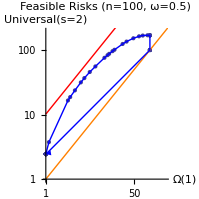
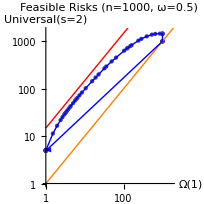
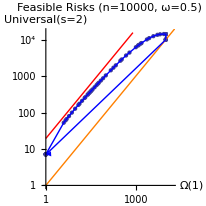
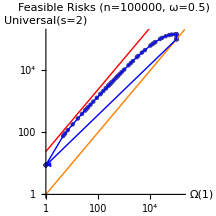

This is a plot to show the results for various values of n on the same graph. The align function rescales the oracle in the argument to match that in the reference set of coordinates.  Of course, all of the xy coordinate pairs (tables) need to be computed on the same grid.

```mathematica
(#⟦1⟧&/@xy[100])/(#⟦1⟧&/@xy[1000])xy[1000]
```

{{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1.,4.9781},{1.,7.46352},{1.,8.48179},{1.,9.09503},{1.,9.34627},{1.,9.54859},{1.,9.61351},{1.,9.6637},{1.,9.71541},{1.,9.76704},{1.,9.81115},{1.,9.83086},{1.,9.89444},{1.,9.92133},{1.,9.92079},{1.,9.91244},{1.,9.87986},{1.,9.81371},{1.14717,11.0705},{2.66802,24.7584},{2.94506,26.5979},{3.63303,31.9382},{4.72828,39.5592},{5.52181,45.2578},{7.02061,53.482},{9.00586,63.6606},{13.4679,82.3334},{15.4683,89.052},{16.5512,93.6673},{19.2555,102.521},{20.9676,108.264},{30.1292,129.591},{35.8269,140.711},{48.5095,156.406},{62.3546,161.448},{73.5121,160.915},{90.9595,152.964},{101.,145.346},{101,145.346},{101,145.346},{101,145.346},{101,145.346},{101,101.023},{101,101},{101,101},{101,101},{101,101},{101,101},{1.01568,4.95336},{1.00034,4.97694}}

```mathematica
Clear[ri];
ri[m_]:=With[
{ri=(#⟦2⟧/(2 Log[m] #⟦1⟧))& /@ (xy[m]),    (*  risk inflation as % of 2 log p *)
rpt=(#⟦1⟧/(2 Log[m]))& /@ (xy[m])                                               (* oracle risk per test *)
},
Sort[Transpose[{rpt,ri}],#1⟦1⟧≤#2⟦1⟧&]
]
```

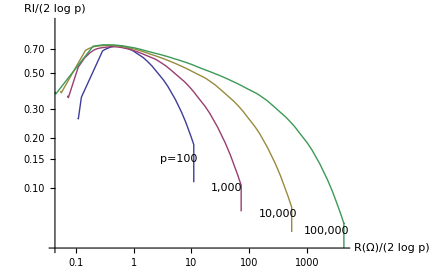

```mathematica
ListLogLogPlot[{ri[100],ri[1000],ri[10000],ri[100000]},
AxesLabel-> {"R(Ω)/(2 log p)","RI/(2 log p)"},
Epilog->{
Text["p=100",Log[{6,0.15}]],
Text["1,000",Log[{40,0.10}]],
Text["10,000",Log[{320,0.07}]],
Text["100,000",Log[{2150,0.055}]]},
Joined->True]
```